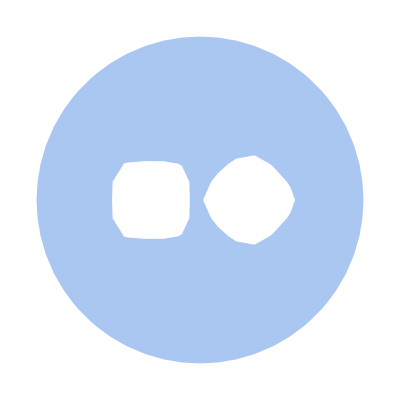

-Graphics-

-Graphics-

16.4438

```mathematica
(*Определение областей*)
outerElectrode=x^2+y^2<=25;
innerElectrodeFirst=0.3Abs[-1.5+x]^1.5+0.3 Abs[y]^1.5<=0.5;
innerElectrodeSecond=0.3Abs[1.5+x]^4+0.3 Abs[y]^4<=0.6;

(*Создание областей*)
outerElectrodeArea=ImplicitRegion[outerElectrode,{x,y}];
areaInnerElectrodeFirst=ImplicitRegion[innerElectrodeFirst,{x,y}];
areaInnerElectrodeSecond=ImplicitRegion[innerElectrodeSecond,{x,y}];
vacantArea=RegionDifference[RegionDifference[outerElectrodeArea,areaInnerElectrodeFirst],areaInnerElectrodeSecond];
Region[vacantArea]
(*Решение уравнения Лапласа*)
laplaceEquation=Laplacian[u[x,y],{x,y}]==0;
conditions={
DirichletCondition[u[x,y]==-5,0.3Abs[-1.5+x]^1.5+0.3 Abs[y]^1.5==0.5],DirichletCondition[u[x,y]==-5,0.3Abs[1.5+x]^4+0.3 Abs[y]^4==0.6],
DirichletCondition[u[x,y]==0,x^2+y^2==25]
};

solution=NDSolve[{laplaceEquation,conditions},u,{x,y}∈vacantArea];

(*Визуализация результатов*)
solutionPlt=ContourPlot[u[x,y]/. First[solution],{x,y}∈vacantArea,Contours->20,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic]
equipotentialPlt=ContourPlot[Evaluate[u[x,y]/. solution]==-4,{x,y}∈vacantArea,Contours->1,PlotLegends->Automatic,ContourStyle->Black];
Show[solutionPlt,equipotentialPlt]

(*Расчет длины*)
points=Cases[Normal@equipotentialPlt,Line[pts_]:>pts,Infinity];
pointPairs=Flatten[points,1];
equipotentialLength=Total@MapThread[EuclideanDistance,{pointPairs,RotateLeft@pointPairs}];
equipotentialLength
```